```mathematica
eulerGen[F_,X0_,tf_,nMax_]:=Module[{h,datalist,prev,next,rate},
h=(tf-X0[[1]])/nMax//N;
For[datalist={X0},
Length[datalist]≤nMax+1,
AppendTo[datalist,next],
prev=Last[datalist];
rate=F@prev;
next=prev+h rate;
];
Return[datalist];
]
```

```mathematica
rk2[F_,X0_,tf_,nMax_]:=Module[{h,datalist,prev,next,rate1,rate2},
h=(tf-X0[[1]])/nMax//N;
For[datalist={X0},
Length[datalist]≤nMax+1,
AppendTo[datalist,next],
prev=Last[datalist];
rate1=F@prev;
rate2=F@(prev+h rate1);
next=prev+h (rate1+rate2)/2;
];
Return[datalist];
]
```

```mathematica
w=10;
β=Sqrt[w-1/4];
rateFunc[{t_,charge_,current_}]={1,current,-w charge-current};
initial={0,1,0};
A=rk2[rateFunc,initial,5,100];
B=eulerGen[rateFunc,initial,5,1000];
```

```mathematica
p=ListPlot[A[[;;,{1,2}]],Joined->True];
q=ListPlot[B[[;;,{1,2}]],Joined->True];
r=Plot[E^(-t/2) Cos[β t],{t,0,5}];
```

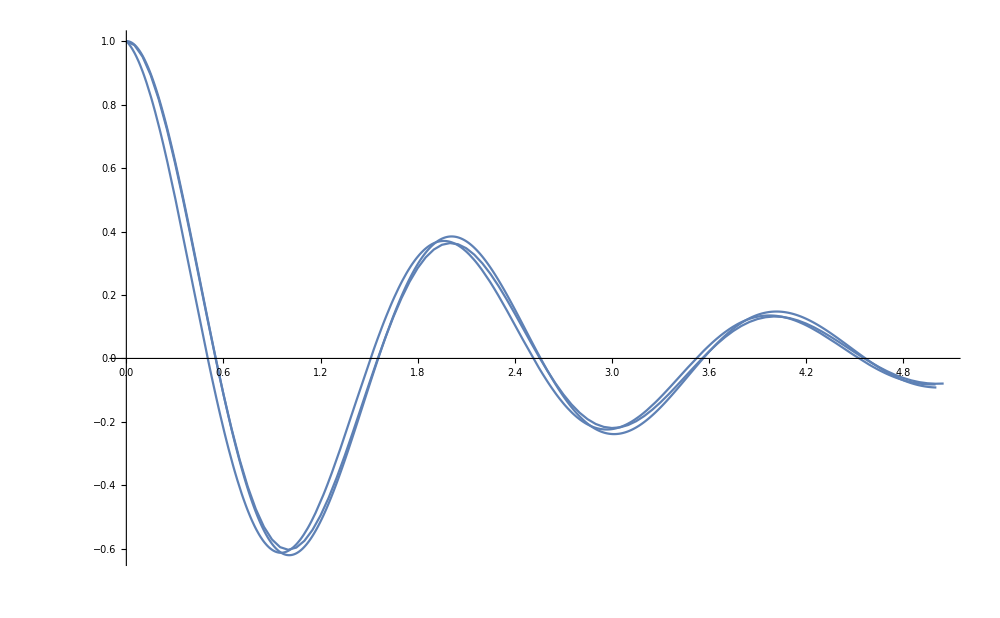

```mathematica
Show[{p,q,r},PlotRange->Full,ImageSize->1000]
```

```mathematica
Clear["Global`*"]
```

X0

Syntax::bktmop: Expression "rk41F_,X0_,tf_,nMax_]" has no opening "[".

```mathematica
rk4[F_,X0_,tf_,nMax_]:=Module[{h,datalist,prev,next,rate1,rate2},
h=(tf-X0[[1]])/nMax//N;
For[datalist={X0},
Length[datalist]≤nMax+1,
AppendTo[datalist,next],
prev=Last[datalist];
rate1=F@prev;
rate2=F@(prev+(h/2) rate1);
rate3=F@(prev+(h/2) rate2);
rate4=F@(prev+h rate3);
next=prev+(h/6) (rate1+2 rate2+2 rate3+rate4);
];
Return[datalist];
]
```